# Projekt

## Czas życia dowolnego systemu bez napraw

Przedstawmy nasz system jako graf zorientowany gdzie każdy wierzchołek odpowiada komponentowi.

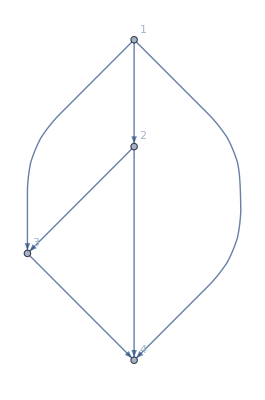

```mathematica
systemGraph=Graph[{1->2,1->3,1->4,2->3,2->4,3->4},VertexLabels->"Name"]
```

Nasz system ma następujące minimalne ścieżki:

```mathematica
rowMinimalPaths=FindPath[systemGraph,1,4,Infinity,All]
```

{{1,4},{1,3,4},{1,2,4},{1,2,3,4}}

Znajdźmy teraz funkcję strukturalną naszego systemu. Wiemy, że można ją uzyskać z wiedzy o minimalnych ścieżkach używając wzoru (strona 583).

```mathematica
getStructureFunction[systemGraph_,systemSource_,systemSink_]:=Module[{rowMinimalPaths,minimalPaths,stateVector,replaceVertexNumbersWithComponentState,pathStates,structureFunction},

replaceVertexNumbersWithComponentState[path_,stateVector_]:= stateVector[[#]]&/@path;

stateVector=Table[x[i],{i,VertexCount[systemGraph]}];
rowMinimalPaths=FindPath[systemGraph,systemSource,systemSink,Infinity,All];
minimalPaths=replaceVertexNumbersWithComponentState[#,stateVector]&/@rowMinimalPaths;
pathStates=Apply[Times,minimalPaths,{1}];
structureFunction=1-Apply[Times,1-pathStates];
structureFunction
]

structureFunction=getStructureFunction[systemGraph,1,4]
```

x[1] x[4]

Ponieważ x[i] ma rozkład bernouliego to x[i]^2 = x[i]

```mathematica
computeReliabilityFunction[structureFunction_]:=Module[{reliabilityFunction},
Clear[p];
reliabilityFunction=Expand[structureFunction]/.a_^p_:>a ;(*remove powers*)
reliabilityFunction/.x->p
]

reliabilityFunction=computeReliabilityFunction[structureFunction]
```

p[1] p[4]

Ma sens, tylko komponenty 1 i 4 mają znaczenie: muszą oba działać. Załóżmy teraz, że czas życia wszystkich komponentów ma rozkład wykładniczy

2 (1-(Piecewise[{{1-ⅇ^(-2 t), t≥0}, {0, True}}])) (Piecewise[{{0, t<0}, {2-2 ⅇ^(-2 t) (-1+ⅇ^(2 t)), t>0}, {Indeterminate, True}}])

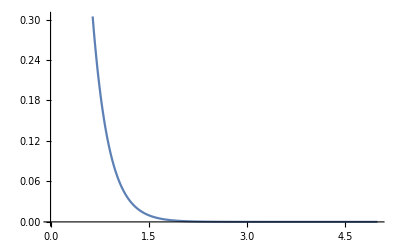

```mathematica
intensity=2;
exponentialTailDistribution=1-CDF[ExponentialDistribution[intensity],t];
componentsTailDistributions=Table[exponentialTailDistribution,VertexCount[systemGraph]];

ComputeSystemLifeTimePDF[componentsTailDistributions_,reliabilityFunction_]:=Module[{systemLifeTimeTailDistribution,systemLifeTimePDF},
For[i=1,i<=Length[componentsTailDistributions],i++,p[i]=componentsTailDistributions[[i]]];
systemLifeTimeTailDistribution=Evaluate[reliabilityFunction];
systemLifeTimePDF=D[1-systemLifeTimeTailDistribution,t];
systemLifeTimePDF
] ;

systemLifeTimePDF=ComputeSystemLifeTimePDF[componentsTailDistributions,reliabilityFunction]
Plot[systemLifeTimePDF,{t,0,5}]
```

Weźmy inny system.

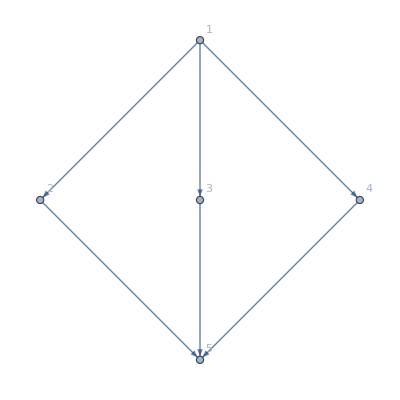

1-(1-x[1] x[2] x[5]) (1-x[1] x[3] x[5]) (1-x[1] x[4] x[5])

p[1] p[2] p[5]+p[1] p[3] p[5]-p[1] p[2] p[3] p[5]+p[1] p[4] p[5]-p[1] p[2] p[4] p[5]-p[1] p[3] p[4] p[5]+p[1] p[2] p[3] p[4] p[5]

9 (1-(Piecewise[{{1-ⅇ^(-2 t), t≥0}, {0, True}}]))^2 (Piecewise[{{0, t<0}, {2-2 ⅇ^(-2 t) (-1+ⅇ^(2 t)), t>0}, {Indeterminate, True}}])-12 (1-(Piecewise[{{1-ⅇ^(-2 t), t≥0}, {0, True}}]))^3 (Piecewise[{{0, t<0}, {2-2 ⅇ^(-2 t) (-1+ⅇ^(2 t)), t>0}, {Indeterminate, True}}])+5 (1-(Piecewise[{{1-ⅇ^(-2 t), t≥0}, {0, True}}]))^4 (Piecewise[{{0, t<0}, {2-2 ⅇ^(-2 t) (-1+ⅇ^(2 t)), t>0}, {Indeterminate, True}}])

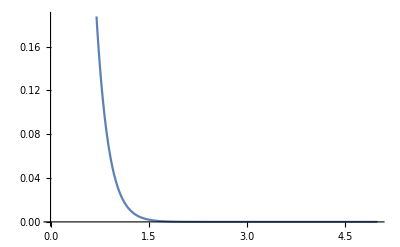

```mathematica
ClearAll;
systemGraph=Graph[{1->2,1->3,1->4,2->5,3->5,4->5},VertexLabels->"Name"]
structureFunction=getStructureFunction[systemGraph,1,5]
reliabilityFunction=computeReliabilityFunction[structureFunction]

componentsTailDistributions=Table[exponentialTailDistribution,VertexCount[systemGraph]];

systemLifeTimePDF=ComputeSystemLifeTimePDF[componentsTailDistributions,reliabilityFunction]
Plot[systemLifeTimePDF,{t,0,5}]
```

```mathematica
Expand[p1*p5*(1-(1-p2)*(1-p3)*(1-p4))]
```

p1 p2 p5+p1 p3 p5-p1 p2 p3 p5+p1 p4 p5-p1 p2 p4 p5-p1 p3 p4 p5+p1 p2 p3 p4 p5